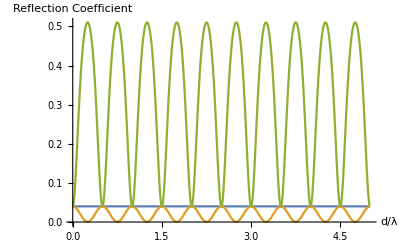

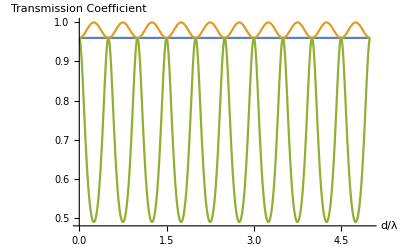

```mathematica
λ=1;n1=1; n3=1.5;
t21 = 2*n1/(n2+n1);
t32 = 2*n2/(n3+n2);
r21 = (n1-n2)/(n2+n1);
r23 = (n3-n2)/(n3+n2);
t12 = 2*n2/(n1+n2);
r12 = (n2-n1)/(n2+n1);
T [d_]:= (n3/n1)*(t21*t32)^2/(1+(r23*r21)^2-2(r23*r21)Cos[4*Pi*d/λ]);

R[d_]:=(r12^2+r23^2+2 r12 r23 Cos[4*Pi*d/λ])/(1+r21^2 r23^2-2r21 r23 Cos[4*Pi*d/λ])

Plot[{R[a]/.{n2-> 1},R[a]/.{n2->1.2},R[a]/.{n2-> 3}},{a,0,5},AxesLabel-> {"d/λ","Reflection Coefficient"}]
Plot[{T[a]/.{n2-> 1},T[a]/.{n2->1.2},T[a]/.{n2-> 3}},{a,0,5},AxesLabel-> {"d/λ","Transmission Coefficient"}]
```